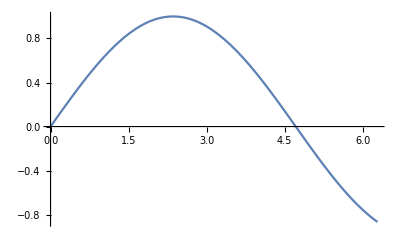

```mathematica
F[x_]:=Sin[2/3 x] ;

a=0;
b = 2π;

Δx = (b-a)/N1;
Plot[F[x],{x,a,b}]
```

```mathematica
N1 = 10000;

Int1 =N[ Sum[(F[a + (k -1)Δx]+F[a+k Δx])/2 Δx,{k,1,N1}],40]
```

2.249999967101318566828961205426102775478

```mathematica
Int2 = Δx/2(F[a]+F[b]+2Sum[F[a+k Δx],{k,1,N1-1}])//Expand;
```

```mathematica
Int1==Int2
```

True

```mathematica
NIntegrate[F[x],{x,a,b},Method->"Trapezoidal"]
```

0.459698

```mathematica
Trap[Func_,x0_,xN_,Ni_]:=Module[
{f=Func,a=x0,b=xN,N1=Ni,Δx,Ans},
Δx = (b-a)/N1;
Ans= Δx/2(f[a]+f[b]+2Sum[f[a+k Δx],{k,1,N1-1}])]
```

```mathematica
Trap[F,a,b,N1]//N
```

0.459698

```mathematica
TrapTol[Func_,x0_,xN_,Tol_]:=Module[
{Ans,f=Func,a=x0,b=xN,ϵ=Tol,try0,try1,n},
n=1;
try0 = Trap[f,a,b,100 2^(n-1)];
n+=1;
try1 = Trap[f,a,b,100 2^(n-1)];

While[Abs[try0-try1]>ϵ,
n+=1;
try0 = try1;
 try1 = Trap[f,a,b,100 2^(n-1)];
];

{try1,n}]
```

```mathematica
Est = N[TrapTol[F,a,b,10^-10],20]
```

{0.45969769411724688646,10.}

```mathematica
Exact = N[Integrate[Sin[x],{x,0,1}],20]
```

0.4596976941318602826

```mathematica
Abs[Est[[1]]-Exact]
```

1.46133961×10^-11